```mathematica
(*pkt={{tiempos de llegada},tiempo de servicio, {ids de los enlaces}}*)

Modelos de colas para análisi de rendimiento en redes de datos.
```

```mathematica
Desarrollar un simulador de una red de paquetes,como la que se muestra en la figura,basado en un modelo de red con colas M/M/1 y representar la evolución de algunos estadísticos de interés obteniendo resultados prácticos que puedan ser contrastados con modelos teóricos de rendimiento y/u otras simulaciones que se puedan realizar en otras prácticas.
```

-Graphics-

```mathematica
La siguientes funciones que simulan los elementos de red que se mencionan a continuación estan basadas en un diseño propio:
```

```mathematica
Parte primera
1. Descomponer la red en elementos sencillos que puedan ser simulados por independiente:

a.Nodo de diversificación de tráfico
```

Parte primera

1. Descomponer elementos en la por puedan que red sencillos ser simulados (independiente:de^2 diversificación tráfico a.Nodo)

```mathematica
La función del nodo de diversificación será dividir el flujo de tráfico entrante en dos flujos salientes en base a una probabilidad. Para ello se propones la siguiente función:
```

```mathematica
Node[in_,prob_,routes_]:=
Module[{x,pkt2},
RoutePkt[pkt_]:=(pkt2=pkt;
x=RandomReal[];If[x<prob,pkt2[[3]]=Append[pkt[[3]],routes[[1]]],pkt2[[3]]=Append[pkt[[3]],routes[[2]]]];
pkt2);
Map[(RoutePkt[#])&,in]
];
FilterLink[lst_,inNode_]:=Map[(If[Last[#[[3]]]==inNode,#,Unevaluated[Sequence[]]])&,lst];
```

```mathematica
b. Nodo de fusión de tráfico

El nodo de fusión de tráfico, fusionará dos o tres flujos entrantes en uno solo, tomando como referencia el tiempo de llegada de cada paquete de cada flujo.La función variará en función del número de flujos entrantes (si estos son dos o tres), la propuesta es la siguiente:
```

de^2 fusión tráfico b.Nodo

```mathematica
flujosConjuntos2[f1_,f2_]:=Module[{f=Sort[Join[f1,f2],Last[#[[1]]]<Last[#2[[1]]]&],n=1},Map[{#[[1]],#[[2]],#[[3]]}&,f]];
```

```mathematica
flujosConjuntos3[f1_,f2_,f3_]:=Module[{f=Sort[Join[f1,f2,f3],Last[#[[1]]]<Last[#2[[1]]]&],n=1},Map[{#[[1]],#[[2]],#[[3]]}&,f]];
```

```mathematica
c. Simulación de la transmisión en un enlace:
Para la simulación de un enlace se tomará en cuenta el tiempo de servicio de cada paquete y el tiempo de propagación del enlace:
```

```mathematica
FifoSchedulling[lst_,tprop_]:=Module[{n,checkTime,lst1,i,arrivals,j,services,p,pkt2,l,sol},i=1;p=1;j=1;checkTime=Last[lst[[1]][[1]]];arrivals=Table[Last[lst[[i++]][[1]]],{i,Length[lst]}];
services=Table[lst[[j++]][[2]],{j,Length[lst]}];
n=1;
lst1=(If[checkTime≥#,checkTime=checkTime+services[[n++]]+tprop,checkTime=#+services[[n++]]+tprop])&/@arrivals;
l=1;
Juntar[pkt_]:=(pkt2=pkt; pkt2[[1]]=Append[pkt[[1]],lst1[[l++]]];pkt2);
sol=Map[(Juntar[#])&,lst];
sol];
```

```mathematica
2. Definir un modelo de paquete a transmitir que permita ser gestionado en los elementos de la
red para poder obtener los datos de la simulación que se necesiten:

La estrcutura de paquete que se ha utilizado es la siguiente:
pkt={{tiempos de llegada},tiempo de servicio, {ids de los enlaces}}.
Para crear los paquetes,se crea un lista de tiempos de llegada y otra de tiempos de servicio que siguen una distribución exponencial:
```

2. a de^2 Definir elementos en gestionado la los modelo paquete permita que ser transmitir un

```mathematica
RndExp[rate_]:=-Log[RandomReal[]]/rate;
```

```mathematica
Función para crear los tiempos de llegada:
```

```mathematica
interArrivals[lambda_,tsim_]:=Table[RndExp[lambda],tsim*lambda];
```

```mathematica
arrivalsTime[lambda_,tsim_]:=Accumulate[interArrivals[lambda,tsim]];
```

```mathematica
Función para crear los tiempos de servicio:
```

```mathematica
serviceTime[mu_,tsim_,lambda_]:=Table[RndExp[mu],tsim*lambda]
```

```mathematica
Función para generar los paquetes de entrada de un determinado nodo:
```

```mathematica
createFlow[lambda_,mu_,id_,tsim_]:=
Module[{arrivals=arrivalsTime[lambda,tsim],services=serviceTime[lambda,mu,tsim],n=1},
Table[{{arrivals[[n]]},services[[n]],{id}},{n,1,tsim*lambda}]];
```

```mathematica
3. Implementar la simulación de la red con los componentes diseñados supuesto que los enlaces
no siguen ningún protocolo (simplemente multiplexación estadística).
```

3. componentes con de diseñados enlaces Implementar la^2 los^2 que red simulación supuesto

```mathematica
Creadas las funciones que permitirán abstracciones de los nodos y enlaces se procederá a realizar la simulación de la red. Antes hay algunas características de la red que hay que parametrizar:
-Tasas de llegadas de los flujos externos (λ=2000 paq/seg) en los enlaces: 1, 2 y 3. 
- Tasas de servicio: 3000 paq/seg.
-Tiempo de propagación: 0.05 seg.
-Tiempo de simulación: 3 seg.
```

```mathematica
lambda1=2;
lambda2=2;
lambda5=2;
mu=3;
Tprop=0.05;
tsim=300;
```

```mathematica
Ext1=createFlow[lambda1,mu,1,tsim];
```

```mathematica
Ext1[[1;;10]]
```

{{{0.818308},0.558759,{1}},{{1.58529},1.32656,{1}},{{1.90846},0.000672816,{1}},{{2.23013},0.240104,{1}},{{2.49982},1.51238,{1}},{{2.73823},0.137945,{1}},{{3.57331},0.259506,{1}},{{3.8532},0.0797965,{1}},{{3.90069},2.60924,{1}},{{5.47541},0.282514,{1}}}

```mathematica
Ext2=createFlow[lambda2,mu,2,tsim];
Ext2[[1;;10]]
```

{{{0.282656},0.170369,{2}},{{0.587487},0.0919695,{2}},{{0.821841},0.453488,{2}},{{1.30915},0.0737823,{2}},{{1.50549},0.164687,{2}},{{1.66245},0.042184,{2}},{{2.72324},1.09513,{2}},{{4.09625},0.0420257,{2}},{{4.9415},0.825788,{2}},{{5.5584},1.16986,{2}}}

```mathematica
Ext5=createFlow[lambda5,mu,5,tsim];
```

```mathematica
Ext5[[1;;10]]
```

{{{0.197556},3.01712,{5}},{{0.37684},0.0184725,{5}},{{0.627694},0.647835,{5}},{{0.97339},0.235571,{5}},{{1.60349},0.618664,{5}},{{1.65569},0.917307,{5}},{{2.87692},1.1461,{5}},{{3.30903},0.242887,{5}},{{3.46989},0.701249,{5}},{{3.49571},0.793035,{5}}}

Salida del nodo1
explizacion

```mathematica
out1=Node[Ext1,1/4,{2,5}];
```

```mathematica
out1[[1;;10]]
```

{{{0.818308},0.558759,{1,5}},{{1.58529},1.32656,{1,5}},{{1.90846},0.000672816,{1,5}},{{2.23013},0.240104,{1,5}},{{2.49982},1.51238,{1,5}},{{2.73823},0.137945,{1,5}},{{3.57331},0.259506,{1,2}},{{3.8532},0.0797965,{1,5}},{{3.90069},2.60924,{1,5}},{{5.47541},0.282514,{1,2}}}

```mathematica
De una muestra de diez paquetes se puede comprobar el correcto funcionamiento de la función de diversificación de tráfico:7/10 paquetes al nodo 5, el cual tenía una probabilidad de 75%.
```

```mathematica
FilterLink[out1[[1;;10]],5]
```

{{{0.818308},0.558759,{1,5}},{{1.58529},1.32656,{1,5}},{{1.90846},0.000672816,{1,5}},{{2.23013},0.240104,{1,5}},{{2.49982},1.51238,{1,5}},{{2.73823},0.137945,{1,5}},{{3.8532},0.0797965,{1,5}},{{3.90069},2.60924,{1,5}}}

```mathematica
Out1to5=FifoSchedulling[FilterLink[out1,5],Tprop];
```

```mathematica
Out1to2=FifoSchedulling[FilterLink[out1,2],Tprop];
```

```mathematica
Ext5[[1;;10]]
```

{{{0.197556},3.01712,{5}},{{0.37684},0.0184725,{5}},{{0.627694},0.647835,{5}},{{0.97339},0.235571,{5}},{{1.60349},0.618664,{5}},{{1.65569},0.917307,{5}},{{2.87692},1.1461,{5}},{{3.30903},0.242887,{5}},{{3.46989},0.701249,{5}},{{3.49571},0.793035,{5}}}

```mathematica
Out1to5[[1;;10]]
```

{{{0.818308,1.42707},0.558759,{1,5}},{{1.58529,2.96185},1.32656,{1,5}},{{1.90846,3.01252},0.000672816,{1,5}},{{2.23013,3.30263},0.240104,{1,5}},{{2.49982,4.86501},1.51238,{1,5}},{{2.73823,5.05295},0.137945,{1,5}},{{3.8532,5.18275},0.0797965,{1,5}},{{3.90069,7.84199},2.60924,{1,5}},{{5.64657,9.37372},1.48174,{1,5}},{{6.03653,9.80299},0.379268,{1,5}}}

```mathematica
flujosConjuntos2[Ext5[[1;;10]],Out1to5[[1;;10]]]
```

{{{0.197556},3.01712,{5}},{{0.37684},0.0184725,{5}},{{0.627694},0.647835,{5}},{{0.97339},0.235571,{5}},{{0.818308,1.42707},0.558759,{1,5}},{{1.60349},0.618664,{5}},{{1.65569},0.917307,{5}},{{2.87692},1.1461,{5}},{{1.58529,2.96185},1.32656,{1,5}},{{1.90846,3.01252},0.000672816,{1,5}},{{2.23013,3.30263},0.240104,{1,5}},{{3.30903},0.242887,{5}},{{3.46989},0.701249,{5}},{{3.49571},0.793035,{5}},{{2.49982,4.86501},1.51238,{1,5}},{{2.73823,5.05295},0.137945,{1,5}},{{3.8532,5.18275},0.0797965,{1,5}},{{3.90069,7.84199},2.60924,{1,5}},{{5.64657,9.37372},1.48174,{1,5}},{{6.03653,9.80299},0.379268,{1,5}}}

```mathematica
Out5=Node[flujosConjuntos2[Ext5,Out1to5],1/2,{2,4}];
```

```mathematica
Out5to2=FifoSchedulling[FilterLink[Out5,2],Tprop];
Out5to4=FifoSchedulling[FilterLink[Out5,4],Tprop];
```

```mathematica
Out2=Node[flujosConjuntos3[Ext2,Out5to2,Out1to2],1/3,{3,4}];
```

```mathematica
Out2[[1;;10]]
```

{{{0.282656},0.170369,{2,4}},{{0.587487},0.0919695,{2,4}},{{0.821841},0.453488,{2,4}},{{1.30915},0.0737823,{2,4}},{{1.50549},0.164687,{2,4}},{{1.66245},0.042184,{2,4}},{{2.72324},1.09513,{2,4}},{{0.197556,3.26468},3.01712,{5,2,4}},{{0.97339,3.55025},0.235571,{5,2,4}},{{3.57331,3.88281},0.259506,{1,2,4}}}

```mathematica
Out2to3=FifoSchedulling[FilterLink[Out2,3],Tprop];
Out2to4=FifoSchedulling[FilterLink[Out2,4],Tprop];
```

```mathematica
Out2to4[[1;;20]]
```

{{{0.282656,0.503026},0.170369,{2,4}},{{0.587487,0.729457},0.0919695,{2,4}},{{0.821841,1.32533},0.453488,{2,4}},{{1.30915,1.44911},0.0737823,{2,4}},{{1.50549,1.72018},0.164687,{2,4}},{{1.66245,1.81237},0.042184,{2,4}},{{2.72324,3.86837},1.09513,{2,4}},{{0.197556,3.26468,6.93549},3.01712,{5,2,4}},{{0.97339,3.55025,7.22106},0.235571,{5,2,4}},{{3.57331,3.88281,7.53056},0.259506,{1,2,4}},{{4.09625,7.62259},0.0420257,{2,4}},{{1.60349,4.21891,8.29125},0.618664,{5,2,4}},{{4.9415,9.16704},0.825788,{2,4}},{{1.90846,3.01252,5.64615,9.21771},0.000672816,{1,5,2,4}},{{5.47541,5.80793,9.55023},0.282514,{1,2,4}},{{3.30903,5.93904,9.84312},0.242887,{5,2,4}},{{6.19657,10.1204},0.227283,{2,4}},{{6.26409,10.1778},0.00739861,{2,4}},{{6.84654,10.424},0.196221,{2,4}},{{7.20844,10.5469},0.0728772,{2,4}}}

```mathematica
Out4=Node[flujosConjuntos2[Out5to4,Out2to4],1,{"S4"}];
```

```mathematica
Out4[[1;;10]]
```

{{{0.37684,0.445313},0.0184725,{5,4,S4}},{{0.282656,0.503026},0.170369,{2,4,S4}},{{0.587487,0.729457},0.0919695,{2,4,S4}},{{0.821841,1.32533},0.453488,{2,4,S4}},{{0.627694,1.32553},0.647835,{5,4,S4}},{{1.30915,1.44911},0.0737823,{2,4,S4}},{{1.50549,1.72018},0.164687,{2,4,S4}},{{1.66245,1.81237},0.042184,{2,4,S4}},{{0.818308,1.42707,2.03583},0.558759,{1,5,4,S4}},{{1.65569,3.00313},0.917307,{5,4,S4}}}

```mathematica
Out4to3=FifoSchedulling[FilterLink[Out4,3],Tprop];
```

Part::partw: Part 1 of {} does not exist.

Last::nolast: {} has zero length and no last element.

```mathematica
Out3=Node[Out2to3,1,{"S3"}];
Se quiere graficar el enlace 1-5
```

-5+el enlace graficar quiere Se

```mathematica
Función para adaptar el tráfico a la función drawTxPRM:
```

```mathematica
AdaptFlow[in_]:=Module[{new={},n=1},
Map[{Last[#[[1]]]-#[[2]]-Tprop,#[[2]],n++,0,0}&,in]];
```

```mathematica
FilterLink[Out2to3[[1;;10]],3]
```

{{{5.5584,6.77826},1.16986,{2,3}},{{1.58529,2.96185,5.59548,8.15483},1.32656,{1,5,2,3}},{{4.10804,6.1229,8.33869},0.133864,{5,2,3}},{{2.49982,4.86501,7.68528,9.90107},1.51238,{1,5,2,3}},{{8.21066,10.8501},0.899032,{2,3}},{{7.99032,8.70898,11.5688},0.66866,{1,2,3}},{{9.04591,14.964},3.34526,{2,3}},{{8.02537,9.63082,15.8859},0.871844,{1,2,3}},{{9.63997,17.1159},1.18,{2,3}},{{9.65642,17.1897},0.0238469,{2,3}}}

```mathematica
AdaptFlow[FilterLink[Out2to3[[1;;10]],3]]
```

{{5.5584,1.16986,1,0,0},{6.77826,1.32656,2,0,0},{8.15483,0.133864,3,0,0},{8.33869,1.51238,4,0,0},{9.90107,0.899032,5,0,0},{10.8501,0.66866,6,0,0},{11.5688,3.34526,7,0,0},{14.964,0.871844,8,0,0},{15.8859,1.18,9,0,0},{17.1159,0.0238469,10,0,0}}

```mathematica
Get["C:\\Users\\Eusk_Aritz\\Desktop\\UNI\\master\\Segundo\\Rendimiento en redes d etelecomunicación\\drawTxPRM.m"]
```

```mathematica
?drawTxPRM`*
```

```mathematica
draw1to5=AdaptFlow[Out1to5];
```

```mathematica
SetIniParDraw[Tprop,0];
```

```mathematica
Manipulate[
Show[DrawWin[tw,ww,8],
Map[DrawPacketTx[#]&,SelectPacketInWin[draw1to5]]],
{tw,0,draw1to5[[Length[draw1to5]]][[1]]-ww},{ww,1,1,300}]
```

Enlace 5-2

```mathematica
draw5to2=AdaptFlow[Out5to2];
```

```mathematica
SetIniParDraw[Tprop,0];
```

```mathematica
Manipulate[
Show[DrawWin[tw,ww,8],
Map[DrawPacketTx[#]&,SelectPacketInWin[draw5to2]]],
{tw,0,draw5to2[[1]]-ww},{ww,1,1,300}]
```

Enlace 2-4

```mathematica
draw2to4=AdaptFlow[Out2to4];
```

```mathematica
SetIniParDraw[Tprop,0]
```

```mathematica
Manipulate[
Show[DrawWin[tw,ww,8],
Map[DrawPacketTx[#]&,SelectPacketInWin[draw2to4]]],
{tw,0,draw2to4[[1]]-ww},{ww,1,1,300}]
```

```mathematica
6 Calcular el retardo medio
```

6 Calcular el medio retardo

```mathematica
Circuito virtual  1-5-2-4-S4
```

-11-S4+Circuito virtual

```mathematica
Out4[[1;;10]]
```

{{{0.37684,0.445313},0.0184725,{5,4,S4}},{{0.282656,0.503026},0.170369,{2,4,S4}},{{0.587487,0.729457},0.0919695,{2,4,S4}},{{0.821841,1.32533},0.453488,{2,4,S4}},{{0.627694,1.32553},0.647835,{5,4,S4}},{{1.30915,1.44911},0.0737823,{2,4,S4}},{{1.50549,1.72018},0.164687,{2,4,S4}},{{1.66245,1.81237},0.042184,{2,4,S4}},{{0.818308,1.42707,2.03583},0.558759,{1,5,4,S4}},{{1.65569,3.00313},0.917307,{5,4,S4}}}

```mathematica
FilterLink2[lst_,inNode_]:=Map[(If[#[[3]]==inNode,#,Unevaluated[Sequence[]]])&,lst];
```

```mathematica
flujo1524S4=FilterLink2[Out4,{1,5,2,4,"S4"}];
```

```mathematica
Length[flujo1524S4]
```

150

```mathematica
retardo [f_]:=Mean[Map[Last[#[[1]]]-First[#[[1]]]&,f]];
```

```mathematica
retardo1524S4=retardo[flujo1524S4]
```

106.976

```mathematica
th[f_]:=Module[{first=First[First[f][[1]]],last=Last[Last[f][[1]]]},Length[f]/(last-first)];
```

```mathematica
th1524S4=th[flujo1524S4]
```

0.313087

```mathematica
Se observa que el retardo es excesivamente grande en el circuito virtual. Se trata de una situación de red saturada, los tiempos de servicio de los paquetes son demasiado altos para poder procesar todos los paquetes sin saturar la red.
```

```mathematica
Circuito Virtual 1-5-4-S4
```

-9-S4+Circuito Virtual

```mathematica
flujo154S4=FilterLink2[Out4,{1,5,4,"S4"}];
```

```mathematica
Length[flujo154S4]
```

223

```mathematica
retardo154S4=retardo[flujo154S4]
```

6.51994

```mathematica
th154S4=th[flujo154S4]
```

0.697239

```mathematica
Circuito Virtual 1-5-2-3-S4
```

-10-S4+Circuito Virtual

```mathematica
flujo1523S4=FilterLink2[Out3,{1,5,2,3,"S3"}];
```

```mathematica
Length[flujo1523S4]
```

76

```mathematica
retardo1523S4=retardo[flujo1523S4]
```

9.03692

```mathematica
th1523S4=th[flujo1523S4]
```

0.242434

```mathematica
Cicuito Virtual 2-4
```

-4+2 Cicuito Virtual

```mathematica
flujo24S4=FilterLink2[Out4,{2,4,"S4"}];
```

```mathematica
Length[flujo24S4]
```

414

```mathematica
retardo24S4=retardo[flujo24S4]
```

88.8456

Circuito Virtual 5 - 2 - 3

```mathematica
flujo523S3=FilterLink2[Out3,{5,2,3,"S3"}];
```

```mathematica
Length[flujo523S3]
```

114

```mathematica
retardo523S3=retardo[flujo523S3]
```

7.45064

```mathematica
th1523S3=th[flujo523S3]
```

0.361225

```mathematica
retardoRed=Mean[Join[
Map[Last[#[[1]]]-First[#[[1]]]&,Out3],
Map[Last[#[[1]]]-First[#[[1]]]&,Out4]]]
```

48.2746

```mathematica
Se puede observar que se consiguen unos retardos excesivamente grandes debido a la saturación de la red.
```

```mathematica
7. Estudiar el tráfico en la red modificando algunos parámetros de entrada:tráfico de entrada a la red,capacidad de los enlaces...
En esta primera prueba se aumentará el parámetro µ a 30 paq/s:
```

```mathematica
lambda1=2;
lambda2=2;
lambda5=2;
mu=30;
Tprop=0.05;
tsim=300;
```

```mathematica
Ext1=createFlow[lambda1,mu,1,tsim];
```

```mathematica
Ext2=createFlow[lambda2,mu,2,tsim];
```

```mathematica
Ext5=createFlow[lambda5,mu,5,tsim];
```

```mathematica
out1=Node[Ext1,1/4,{2,5}];
```

```mathematica
Out1to5=FifoSchedulling[FilterLink[out1,5],Tprop];
```

```mathematica
Out1to2=FifoSchedulling[FilterLink[out1,2],Tprop];
```

```mathematica
Out5=Node[flujosConjuntos2[Ext5,Out1to5],1/2,{2,4}];
```

```mathematica
Out5to2=FifoSchedulling[FilterLink[Out5,2],Tprop];
Out5to4=FifoSchedulling[FilterLink[Out5,4],Tprop];
```

```mathematica
Out2=Node[flujosConjuntos3[Ext2,Out5to2,Out1to2],1/3,{3,4}];
```

```mathematica
Out2to3=FifoSchedulling[FilterLink[Out2,3],Tprop];
Out2to4=FifoSchedulling[FilterLink[Out2,4],Tprop];
```

```mathematica
Out3=Node[Out2to3,1,{"S3"}];
Out4=Node[flujosConjuntos2[Out5to4,Out2to4],1,{"S4"}];
```

```mathematica
retardoRed=Mean[Join[
Map[Last[#[[1]]]-First[#[[1]]]&,Out3],
Map[Last[#[[1]]]-First[#[[1]]]&,Out4]]]
```

40.7842

```mathematica
Se observa que la saturación de red es menor respecto al apartado anterior
```

Otro ejemplo
LLevar la red a una saturación extrema

```mathematica
lambda1=3;
lambda2=3;
lambda5=3;
mu=3;
Tprop=0.05;
tsim=300;
Ext1=createFlow[lambda1,mu,1,tsim];
Ext2=createFlow[lambda2,mu,2,tsim];
Ext5=createFlow[lambda5,mu,5,tsim];
out1=Node[Ext1,1/4,{2,5}];
Out1to5=FifoSchedulling[FilterLink[out1,5],Tprop];
Out1to2=FifoSchedulling[FilterLink[out1,2],Tprop];
Out5=Node[flujosConjuntos2[Ext5,Out1to5],1/2,{2,4}];
Out5to2=FifoSchedulling[FilterLink[Out5,2],Tprop];
Out5to4=FifoSchedulling[FilterLink[Out5,4],Tprop];
Out2=Node[flujosConjuntos3[Ext2,Out5to2,Out1to2],1/3,{3,4}];
Out2to3=FifoSchedulling[FilterLink[Out2,3],Tprop];
Out2to4=FifoSchedulling[FilterLink[Out2,4],Tprop];
Out3=Node[Out2to3,1,{"S3"}];
Out4=Node[flujosConjuntos2[Out5to4,Out2to4],1,{"S4"}];
```

```mathematica
retardoRed=Mean[Join[
Map[Last[#[[1]]]-First[#[[1]]]&,Out3],
Map[Last[#[[1]]]-First[#[[1]]]&,Out4]]]
```

45.9423

Parte Cuarta
Utilizando las funciones de modelado de redes de colas

```mathematica
lambda1=2;
lambda2=2;
lambda5=2;
```

```mathematica
Vector de llegadas:
```

```mathematica
γ={
lambda1*1/4,(* ENLACE A *)
lambda1*3/4,(* ENLACE B*)
lambda2*1/3,(* ENLACE F*)
lambda2*2/3,(* ENLACE E*)
lambda5*1/2,(* ENLACE C*)
lambda5*1/2    (* ENLACE D*)
};
```

```mathematica
Matriz de probabilidades de rutado :
```

```mathematica
r={
{0,0,1/3,2/3,0,0}, (* A *)
{0,0,0,0,1/2,1/2}, (* B *)
{0,0,0,0,0,0}, (* F *)
{0,0,0,0,0,0}, (* E *)
{0,0,0,0,0,0}, (* C *)
{0,0,1/3,2/3,0,0} (* D *)
};
```

```mathematica
Vector de tiempos de servicio :
```

```mathematica
μ={3,3,3,3,3,3};
capacidad:
```

```mathematica
c={1,1,1,1,1,1};
```

Red de colas abiertas :

```mathematica
net=QueueingNetworkProcess[γ,r,μ,c];
```

```mathematica
Se pueden obtener los parámetros correspondientes a cada una de las colas de la siguiente forma:
```

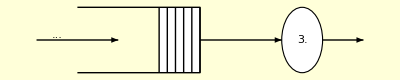
-Graphics- | 
Basic Properties | 
NetworkType | Open
NodeCount | 6.
SelectedNode | 1.
Performance Measures | 
MeanSystemSize | 0.2
MeanSystemTime | 0.4
MeanQueueSize | 0.0333333
MeanQueueTime | 0.0666667

```mathematica
QueueProperties[{net,1}]//N (* ENLACE A*)
```

```mathematica
QueueProperties[{net,2}]//N (* ENLACE B*)
```

-Graphics- | 
Basic Properties | 
NetworkType | Open
NodeCount | 6.
SelectedNode | 2.
Performance Measures | 
MeanSystemSize | 1.
MeanSystemTime | 0.666667
MeanQueueSize | 0.5
MeanQueueTime | 0.333333

```mathematica
QueueProperties[{net,3}]//N (* ENLACE F*)
```

-Graphics- | 
Basic Properties | 
NetworkType | Open
NodeCount | 6.
SelectedNode | 3.
Performance Measures | 
MeanSystemSize | 0.894737
MeanSystemTime | 0.631579
MeanQueueSize | 0.422515
MeanQueueTime | 0.298246

```mathematica
QueueProperties[{net,4}]//N (* ENLACE E*)
```

-Graphics- | 
Basic Properties | 
NetworkType | Open
NodeCount | 6.
SelectedNode | 4.
Performance Measures | 
MeanSystemSize | 17.
MeanSystemTime | 6.
MeanQueueSize | 16.0556
MeanQueueTime | 5.66667

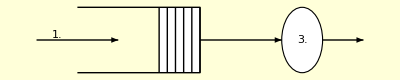
-Graphics- | 
Basic Properties | 
NetworkType | Open
NodeCount | 6.
SelectedNode | 5.
Performance Measures | 
MeanSystemSize | 1.4
MeanSystemTime | 0.8
MeanQueueSize | 0.816667
MeanQueueTime | 0.466667

```mathematica
QueueProperties[{net,5}]//N (* ENLACE C*)
```

```mathematica
QueueProperties[{net,6}]//N (* ENLACE D*)
```

-Graphics- | 
Basic Properties | 
NetworkType | Open
NodeCount | 6.
SelectedNode | 6.
Performance Measures | 
MeanSystemSize | 1.4
MeanSystemTime | 0.8
MeanQueueSize | 0.816667
MeanQueueTime | 0.466667

```mathematica
Se puede simular la red creada utilizando la función RandomFunction, indicando el tiempo de inicio y el tiempo final. En este caso se va a simular la red inicial sin modificaciones de rutado. Como tiempo inicial se va a utilizar 0, y como tiempo final 100.
```

```mathematica
simu=RandomFunction[net,{0,100}]
```

TemporalData[…]

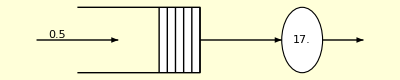
-Graphics- | 
Basic Properties | 
DataSource | QueueingNetwork
NodeCount | 6.
SelectedNode | 1.
Performance Measures | 
MeanSystemSize | 0.163455
MeanSystemTime | 0.3024
MeanQueueSize | 0.0253383
MeanQueueTime | 0.046877

```mathematica
QueueProperties[{simu,1}]//N
```

```mathematica
retardoB=QueueProperties[{simu,2}][[1]][[8]][[2]]
```

0.723396

```mathematica
retardoC=QueueProperties[{simu,5}][[1]][[8]][[2]]
```

0.810952

```mathematica
retardoE=QueueProperties[{simu,4}][[1]][[8]][[2]]
```

3.94129

```mathematica
retardo1524simu=delayB+delayC+delayE
```

3.91897